```mathematica
datastring= "1 WESTERN_CAPE FEMALE 48
2 FREE_STATE MALE 85
3 GAUTENG MALE 79
4 KWAZULU-NATAL FEMALE 46
5 KWAZULU-NATAL MALE 74
6 KWAZULU-NATAL FEMALE 63
7 KWAZULU-NATAL FEMALE 81
8 KWAZULU-NATAL FEMALE 80
9 KWAZULU-NATAL MALE 80
10 WESTERN_CAPE FEMALE 82
11 KWAZULU-NATAL MALE 86
12 WESTERN_CAPE MALE 57
13 KWAZULU-NATAL MALE 60
14 FREE_STATE MALE 55 
15 FREE_STATE MALE 77
16 GAUTENG MALE 49 
17 GAUTENG MALE 52
18 KWAZULU-NATAL MALE 70
19 KWAZULU-NATAL FEMALE 71
20 KWAZULU-NATAL MALE 79
21 KWAZULU-NATAL FEMALE 86
22 KWAZULU-NATAL MALE 91
23 KWAZULU-NATAL FEMALE 73
24 KWAZULU-NATAL FEMALE 79
25 GAUTENG MALE 50";
```

```mathematica
data = ImportString[datastring, "Table"]
```

{{1,WESTERN_CAPE,FEMALE,48},{2,FREE_STATE,MALE,85},{3,GAUTENG,MALE,79},{4,KWAZULU-NATAL,FEMALE,46},{5,KWAZULU-NATAL,MALE,74},{6,KWAZULU-NATAL,FEMALE,63},{7,KWAZULU-NATAL,FEMALE,81},{8,KWAZULU-NATAL,FEMALE,80},{9,KWAZULU-NATAL,MALE,80},{10,WESTERN_CAPE,FEMALE,82},{11,KWAZULU-NATAL,MALE,86},{12,WESTERN_CAPE,MALE,57},{13,KWAZULU-NATAL,MALE,60},{14,FREE_STATE,MALE,55},{15,FREE_STATE,MALE,77},{16,GAUTENG,MALE,49},{17,GAUTENG,MALE,52},{18,KWAZULU-NATAL,MALE,70},{19,KWAZULU-NATAL,FEMALE,71},{20,KWAZULU-NATAL,MALE,79},{21,KWAZULU-NATAL,FEMALE,86},{22,KWAZULU-NATAL,MALE,91},{23,KWAZULU-NATAL,FEMALE,73},{24,KWAZULU-NATAL,FEMALE,79},{25,GAUTENG,MALE,50}}

```mathematica
Length[data]
```

25

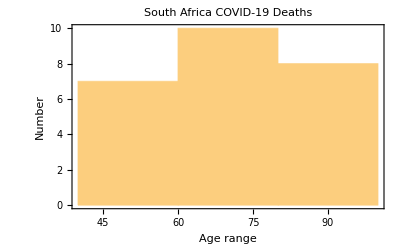

```mathematica
Histogram[data[[All, 4]]
, Frame->True
, FrameLabel->{"Age range", "Number"}
, PlotLabel->"South Africa\nCOVID-19 Deaths"
]
```

```mathematica
364058/(364058+1586986)*1000.
```

186.597